```mathematica
PlotSurf[surffname_]:=Module[{surfs,surfshapes},
surfs=Import[surffname, "Table",HeaderLines->9, "FieldSeperators"->" ", "LineSeperators"->"\n"];
surfshapes=Flatten@Table[Line[{{s[[2]],s[[3]]},{s[[4]],s[[5]]}}],{s,surfs}];
Graphics[Join[{Directive[{Thin,Red}]},surfshapes],ImageSize->Large]
]
```

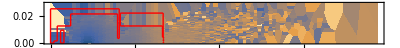

-Graphics-

-Graphics-

```mathematica
data=Import["/home/cal/Documents/DSMC_Simulations/5_29_20_cold_guided/flow_4.00000_gap_0.00100_len_0.04000_T1_2.00000_T2_0.50000/data/exitstats_omega_0.00000_M_191.0_zmax_0.10609_pflip_0.10000.csv","Table",HeaderLines->1,"FieldSeparators"->","];
surfs=PlotSurf["/home/cal/Documents/DSMC_Simulations/5_29_20_cold_guided/flow_4.00000_gap_0.00100_len_0.04000_T1_2.00000_T2_0.50000/data/cell.surfs"];
data=Select[data,#[[3]]>0.00001&];
data=data/.{a_,b_,c_,d_,e_,f_,g_,h_,i_,j_}/;c<0.0001->{a,b,-10000,-10000,-10000,-10000,-10000,-10000,-10000,-10000};
z=data[[;;,1]];
r=data[[;;,2]];
n=data[[;;,3]];
t=data[[;;,4]];
tσ=√data[[;;,5]];
vr=data[[;;,6]];
vz=data[[;;,7]];
vrσ=√data[[;;,8]];
vzσ=data[[;;,9]];
cov=data[[;;,10]];
colls = data[[;;,11]];
d=colls;
Show[ListDensityPlot[Transpose@{r,z,d},PlotRange->{(Sort@DeleteDuplicates[d])[[2]],Max@d},InterpolationOrder->0,PlotLegends->Automatic,AspectRatio->(Max@z)/(Max@r),ImageSize->Full],surfs]
Show[ListDensityPlot[Transpose@{r,z,d},PlotRange->{(Sort@DeleteDuplicates[d])[[2]],Max@d},InterpolationOrder->0,PlotLegends->Automatic,AspectRatio->(Max@z)/(Max@r),ImageSize->Full],surfs]
```

```mathematica
data[[10]]
```

{0.00015,0.05075,3132.,0.00867174,0.0000511448,0.681836,4.3642,46.8047,97.6335,11.0604,2668.31,4.84341×10^6,0.0000407378,2.23151×10^-9}